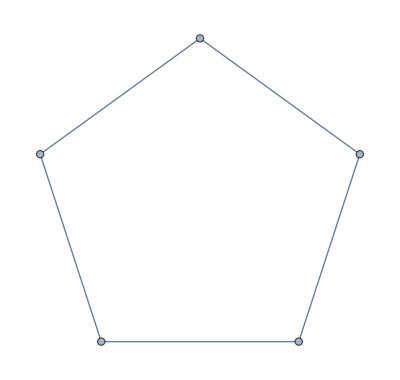

```mathematica
g1 = Graph [{1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5, 5 <-> 1}]
```

```mathematica
ref=PlanarGraphQ[g1]
```

True



```mathematica
g2=CompleteGraph[{5}]
```

```mathematica
ref=PlanarGraphQ[g2]
```

False

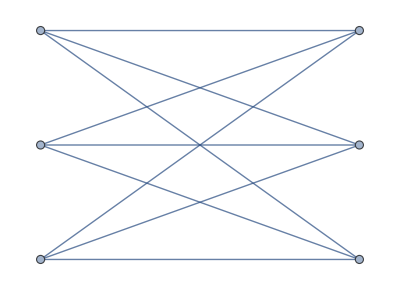

```mathematica
g3=CompleteGraph[{3,3}]
```

```mathematica
ref=PlanarGraphQ[g3]
```

False

False

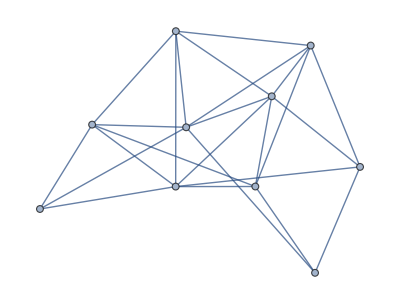

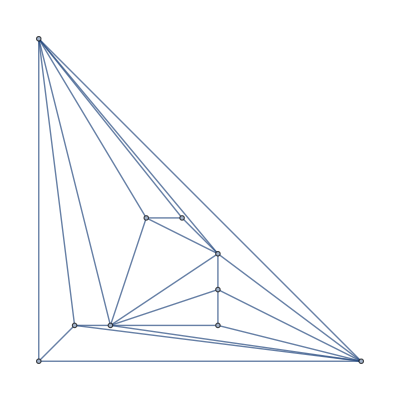

```mathematica
False

n = 10;
e = RandomInteger[{n, 3* n - 6}];
g = RandomGraph[{n, e}]
While[!PlanarGraphQ[g], g = RandomGraph[{n, e}]]
GraphPlot[g, Method->"PlanarEmbedding"]
```